```mathematica
(* For comments see the 'arith_visibility' notebook. *)
```

```mathematica
(* This notebook needs the aforementioned one. GM == GoldenMean. *)
```

```mathematica
ClearAll[algnormGM,ModuloGM,GCDGM];
ClearAll[FindTupleGM,pCond1GM,pCond2GM];
```

```mathematica
algnormGM[{a_Integer, b_Integer}]:=a^2+a*b-b^2;
```

```mathematica
ModuloGM[{a1_Integer, b1_Integer}, {a2_Integer, b2_Integer}] :=
  Block[{norm,alpha, beta},
norm = algnormGM[{a2,b2}] ;
alpha = Round[(a1*a2-b1*b2+a1*b2)/norm];
beta = Round[(b1*a2-a1*b2)/norm];
Return[{a1-(alpha*a2+beta*b2),
b1-(alpha*b2+beta*(a2+b2))}];
  ];
```

```mathematica
GCDGM[{a1_Integer, b1_Integer}, {a2_Integer, b2_Integer}] :=
  Block[{x, y, z},
x = {a1, b1};
y = {a2, b2};
While[y != {0, 0},
z = y;
y = ModuloGM[x, y];
x = z;
];
Return[x]
  ];
```

```mathematica
Map[GCDGM[Part[#,1],Part[#,2]]&,RandomInteger[{1,400},{50,2,2}]]
```

{{-2,-3},{0,1},{-1,-2},{1,1},{-1,0},{-5,-8},{3,5},{-5,-8},{-8,-13},{0,1},{8,13},{5,8},{13,21},{5,8},{-1,-1},{-8,-13},{0,-1},{-3,-5},{-1,-1},{1,1},{1,0},{8,13},{2,3},{2,3},{-3,-5},{-2,2},{26,42},{1,2},{-8,-13},{-1,-2},{-1,0},{1,1},{2,3},{-3,-5},{1,0},{8,13},{8,13},{5,8},{13,21},{5,-3},{8,13},{1,4},{-3,-5},{1,1},{3,5},{-2,-3},{-5,-8},{2,3},{-2,-3},{3,5}}

```mathematica
FindTupleGM[p_Integer]:=Block[{x,y},
y=0;
While[True,x=(-y+Sqrt[5*y^2+4*p])/2;
If[Element[x,Integers],Return[{x,y}]];
x=(-y-Sqrt[5*y^2+4*p])/2;
If[Element[x,Integers],Return[{x,y}]];
y=y+1;]];
```

```mathematica
pCond1GM[p_Integer]:=Mod[p-1,5]==0||Mod[p+1,5]==0;
pCond2GM[p_Integer]:=Mod[p-2,5]==0||Mod[p+2,5]==0;
```

```mathematica
Map[FindTupleGM,Select[Table[Prime[i],{i,1,100}],pCond1GM]]
```

{{3,1},{4,1},{5,1},{5,2},{6,1},{7,2},{7,3},{8,1},{8,3},{9,1},{9,4},{10,1},{11,1},{11,2},{11,4},{11,5},{12,5},{13,1},{13,2},{13,3},{13,6},{14,3},{15,1},{14,5},{15,2},{15,4},{16,1},{15,7},{16,5},{17,3},{17,5},{17,7},{19,1},{18,5},{18,7},{19,3},{20,1},{19,4},{19,5},{19,6},{19,8},{21,1},{21,2},{20,7},{20,9},{21,4},{21,5},{22,3}}

```mathematica
Map[algnormGM,%]
```

{11,19,29,31,41,59,61,71,79,89,101,109,131,139,149,151,179,181,191,199,211,229,239,241,251,269,271,281,311,331,349,359,379,389,401,409,419,421,431,439,449,461,479,491,499,509,521,541}

```mathematica
ClearAll[ConjGM,MultGM,SquareGM,CubeGM];
ClearAll[divTest2Free1GM,divTest2Free2GM];
ClearAll[visibility2FreeGM];
```

```mathematica
ConjGM[{a_Integer, b_Integer}]:={a+b,-b};
```

```mathematica
MultGM[{a1_Integer, b1_Integer}, {a2_Integer, b2_Integer}]:={a1*a2+b1*b2,a1*b2+b1*a2+b1*b2};
SquareGM[{a_Integer,b_Integer}]:={a^2+b^2,b*(2*a+b)};
CubeGM[{a_Integer,b_Integer}]:={a^3+3*a*b^2+b^3,b*(3*a^2+3*a*b+2*b^2)};
```

```mathematica
divTest2Free1GM[{m_Integer,n_Integer},p_Integer]:=Block[{t,a1,a2,b1,b2},
t=FindTupleGM[p]; (* algnorm(t) = p *)
a1 = SquareGM[t]; (* a1 = t^2 *)
a2 = SquareGM[ConjGM[t]]; (* a2 = conj(t)^2 *)
b1=MultGM[{m,n},a1]; (* b1 = x * a1 *)
b2=MultGM[{m,n},a2]; (* b2 = x * a2 *)
Return[IsDivComp[b1,p^2]||IsDivComp[b2,p^2]];
];
```

```mathematica
divTest2Free2GM[{m_Integer,n_Integer},p_Integer]:=IsDivComp[{m,n},p^2];
```

```mathematica
visibility2FreeGM[{m_Integer,n_Integer}]:=Block[{norm,primes,c},
If[Mod[m,5]==0&&Mod[n,5]==0,Return[False]];
norm=algnormGM[{m,n}];
If[Abs[norm]==1,Return[True]];
primes=Map[Part[#,1]&,FactorInteger[Abs[norm]]];
c=Catch[Flatten[Map[Function[t,
If[pCond1GM[t],If[divTest2Free1GM[{m,n},t],Throw[False]],
If[pCond2GM[t],If[divTest2Free2GM[{m,n},t],Throw[False]]]]
],primes],1]];
If[c===False,Return[False],Return[True]];
];
```

```mathematica
ClearAll[vTableGM,miEmbedGM,vDrawGM];
```

```mathematica
vTableGM[r_Integer]:=Flatten[Table[{i,j},{i,-r,r},{j,-r,r}],1];
```

```mathematica
miEmbedGM[{a_Integer,b_Integer}]:=a*{1,1}+b*{GoldenRatio,1-GoldenRatio};
```

```mathematica
vDrawGM[in_,axes_:True,pstyle_:Automatic]:=ListPlot[Map[miEmbedGM,in],Axes->axes,PlotStyle->pstyle,AspectRatio->Automatic];
```

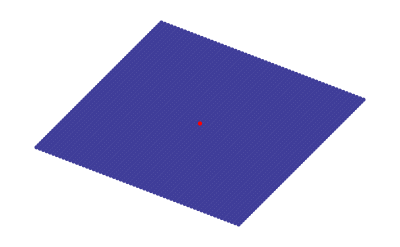

```mathematica
Show[vDrawGM[vTableGM[30],False],Graphics[{Red,Point[{0,0}]}]]
```

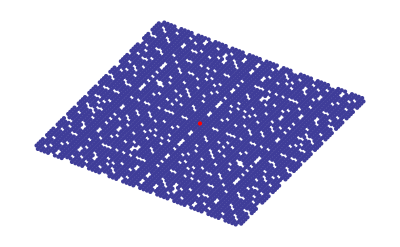

```mathematica
Show[vDrawGM[Select[vTableGM[30],visibility2FreeGM],False],Graphics[{Red,Point[{0,0}]}]]
```

```mathematica
ClearAll[checkBoxGM,cutBoxGM];
```

```mathematica
checkBoxGM[in_,xmax_,ymax_]:=Block[{mi},
mi=miEmbedGM[in];
Return[Abs[Part[mi,1]]≤xmax&&Abs[Part[mi,2]]≤ymax]];
```

```mathematica
cutBoxGM[in_,xmax_,ymax_]:=Select[in,checkBoxGM[#,xmax,ymax]&];
```

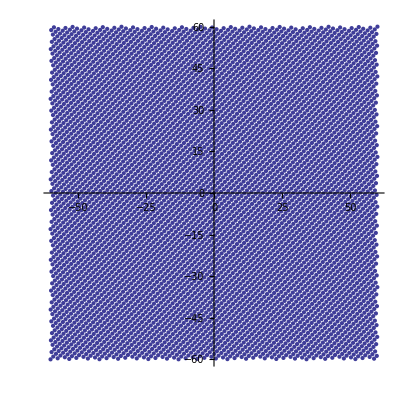

```mathematica
Function[range,vDrawGM[cutBoxGM[vTableGM[range],range,range]]][60]
```

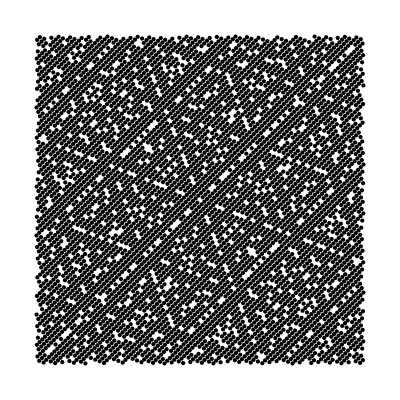

```mathematica
Function[range,vDrawGM[cutBoxGM[Select[vTableGM[range],visibility2FreeGM],
range,range],False,{PointSize[Tiny],Black}]][60]
```

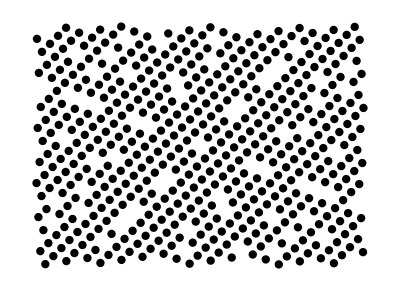

```mathematica
Function[range,vDrawGM[cutBoxGM[Select[vTableGM[range],visibility2FreeGM],
range*0.55,range*0.55*0.73],False,{PointSize[0.015],Black}]][37]
```

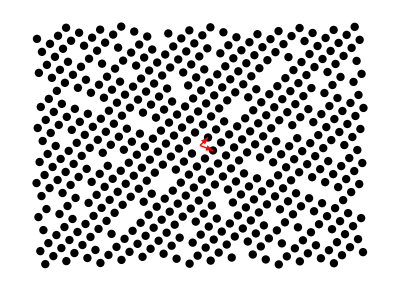

```mathematica
Show[%,Graphics[{Red,Arrowheads[0.011],
Arrow[{{0,0},miEmbedGM[{1,0}]}],Arrow[{{0,0},miEmbedGM[{0,1}]}]}]]
```

```mathematica
Export["/homes/tjakobi/out1.eps",Out[161]]
```

/homes/tjakobi/out1.eps

```mathematica
N[1/(Zeta[2]*DirichletL[5,3,2])]
```

0.860829

```mathematica
Table[DirichletCharacter[5,3,n],{n,0,10}]
```

{0,1,-1,-1,1,0,1,-1,-1,1,0}

```mathematica
If[Not[ValueQ[ArithFast]],Function[x,N[Length[Select[vTableGM[x],visibility2FreeGM]]/Length[vTableGM[x]]]][180]]
```

0.859079

```mathematica
ClearAll[DivGM,IsDivGM,denomGM,pTest1GM,factorGM,testFactorGM];
```

```mathematica
DivGM[{a1_Integer, b1_Integer}, {a2_Integer, b2_Integer}]:=Block[{n,x,y},
n=algnormGM[{a2,b2}];
x=a1*(a2+b2)-b1*b2;
y=a2*b1-a1*b2;
{Divide[x,n],Divide[y,n]}
];
```

```mathematica
IsDivGM[{a1_Integer, b1_Integer}, {a2_Integer, b2_Integer}]:=Block[{n,x,y},
n=algnormGM[{a2,b2}];
x=a1*(a2+b2)-b1*b2;
y=a2*b1-a1*b2;
Mod[x,n]==0&&Mod[y,n]==0
];
```

```mathematica
denomGM[{{a_Integer,b_Integer},c_Integer}]:=Block[{x,g},
x={2*a+b,a+3*b};
g=GCDGM[{c,0},x];
Return[DivGM[{c,0},g]];
];
```

```mathematica
pTest1GM[{m_Integer,n_Integer},p_Integer]:=Block[{t},
t=FindTupleGM[p];
Select[{t,ConjGM[t]},IsDivGM[{m,n},#]&]
];
```

```mathematica
factorGM[{m_Integer,n_Integer}]:=Block[{norm,nprimes},
norm=algnormGM[{m,n}];
If[Abs[norm]==1,Return[{}]];
nprimes=Map[Part[#,1]&,FactorInteger[Abs[norm]]];
Flatten[Map[Function[x,
If[Mod[x,5]==0,{{-1,2}}, (* if we encounter the prime '5', we have a factor of (-1+2*tau) *)
If[pCond2GM[x],{{x,0}},
If[pCond1GM[x],pTest1GM[{m,n},x]]]]
],nprimes],1]
];
```

```mathematica
testFactorGM[{m_Integer,n_Integer}]:=Block[{},
Map[IsDivGM[{m,n},#]&,factorGM[{m,n}]]];
```

```mathematica
Union[Flatten[Map[Union[testFactorGM[#]]&,Flatten[RandomInteger[{1,800},{300,1,2}],1]],1]]
```

{True}

```mathematica
ClearAll[BasisGM,DualGM,intensityGM,vqTableRecipGM];
```

```mathematica
BasisGM={{1,GoldenRatio},
{1,1-GoldenRatio}};
```

```mathematica
DualGM=FullSimplify[Inverse[Transpose[BasisGM]]];
DualGM//MatrixForm
```

((-1+GoldenRatio)/(√5) | 1/(√5)
GoldenRatio/(√5) | -1/(√5))

```mathematica
Det[BasisGM]
```

1-2 GoldenRatio

```mathematica
intensityGM[{m_Integer,n_Integer}]:=Block[{f,prod},
If[m==0&&n==0,Return[0]];
f=1/(Det[BasisGM]*Zeta[2]*DirichletL[5,3,2]);
prod=Apply[Times,Map[1/(algnormGM[#]^2-1)&,factorGM[{m,n}]]];
Return[(f*prod)^2];
];
```

```mathematica
vqTableRecipGM[r_,s_]:=Union[Flatten[ParallelTable[{{-a+2*b,2*a+b},5*c}/GCD[-a+2*b,2*a+b,5*c],
{c,1,s},{a,-r,r},{b,-r,r}],2]];
```

```mathematica
ClearAll[divTest3Free1GM,divTest3Free2GM,visiblity3FreeGM];
```

```mathematica
divTest3Free1GM[{m_Integer,n_Integer},p_Integer]:=Block[{t,a1,a2,b1,b2},
t=FindTupleGM[p]; (* algnorm(t) = p *)
a1=CubeGM[t]; (* a1 = t^3 *)
a2=CubeGM[ConjGM[t]]; (* a2 = conj(t)^3 *)
b1=MultGM[{m,n},a1]; (* b1 = x * a1 *)
b2=MultGM[{m,n},a2]; (* b2 = x * a2 *)
Return[IsDivComp[b1,p^3]||IsDivComp[b2,p^3]];
];
```

```mathematica
divTest3Free2GM[{m_Integer,n_Integer},p_Integer]:=IsDivComp[{m,n},p^3];
```

```mathematica
CubeGM[{-1,2}]
```

{-5,10}

```mathematica
visiblity3FreeGM[{m_Integer,n_Integer}]:=Block[{norm,primes,c},
If[IsDivGM[{m,n},{-5,10}],Return[False]]; (* check if divisible by (-1+2*tau)^3 *)
norm=algnormGM[{m,n}];
If[Abs[norm]==1,Return[True]];
primes=Map[Part[#,1]&,FactorInteger[Abs[norm]]];
c=Catch[Flatten[Map[Function[t,
If[pCond1GM[t],If[divTest3Free1GM[{m,n},t],Throw[False]],
If[pCond2GM[t],If[divTest3Free2GM[{m,n},t],Throw[False]]]]
],primes],1]];
If[c===False,Return[False],Return[True]];
];
```

```mathematica
ClearAll[miEmbedGMR,intensityPlotGM,testCutGM];
```

```mathematica
miEmbedGMR[{{a_Integer,b_Integer},c_Integer}]:=(BasisGM.{a,b})/c;
```

```mathematica
intensityPlotGM[in_,scaleFunc_,cutFunc_]:=Block[{temp},
temp=Map[{#,denomGM[#]}&,Select[in,cutFunc]];
Graphics[
Map[Circle[N[miEmbedGMR[Part[#,1]]],scaleFunc[N[intensityGM[Part[#,2]]]]]&,
Select[temp,visiblity3FreeGM[Part[#,2]]&]]
]
];
```

```mathematica
testCutGM[x_]:=Norm[N[miEmbedGMR[x]]]≤1.5;
```

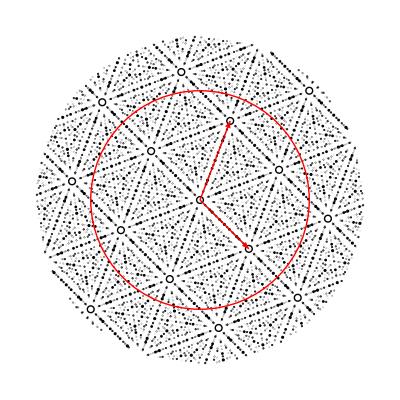

```mathematica
Show[intensityPlotGM[vqTableRecipGM[25,11],Sqrt[Sqrt[#]]*0.05&,testCutGM],
Graphics[{Red,Circle[{0,0},1],
Arrow[{{0,0},DualGM.{0,1}}],Arrow[{{0,0},DualGM.{1,0}}]}]]
```

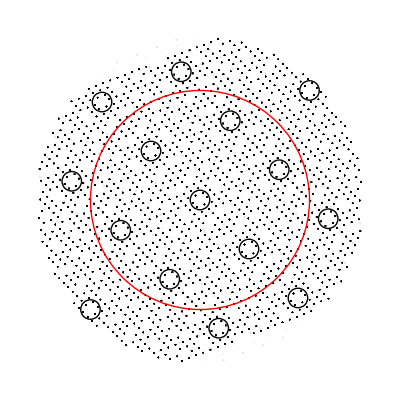

```mathematica
Show[intensityPlotGM[vqTableRecipGM[25,11],#*0.6&,testCutGM],
Graphics[{Red,Circle[{0,0},1]}]]
```

```mathematica
lvec1GM:={GoldenRatio-1,GoldenRatio}/Sqrt[5];
lvec2GM:={1,-1}/Sqrt[5];
```

```mathematica
(* Box clipping test, currently using the basis vectors of the reciprocal lattice. *)
(* Two times two fundamental domains are cut. *)
clipCutGM[x_]:=Block[{y},
y=N[miEmbedGMR[x]];
If[clipEps+clipLinePoint[lvec2GM+{0,0},lvec2GM+lvec1GM,y]<0,Return[False]];
If[clipEps+clipLinePoint[-lvec2GM+lvec1GM,-lvec2GM+{0,0},y]<0,Return[False]];
If[clipEps+clipLinePoint[-lvec1GM+{0,0},-lvec1GM+lvec2GM,y]<0,Return[False]];
If[clipEps+clipLinePoint[lvec1GM+lvec2GM,lvec1GM+{0,0},y]<0,Return[False]];
Return[True];
];
```

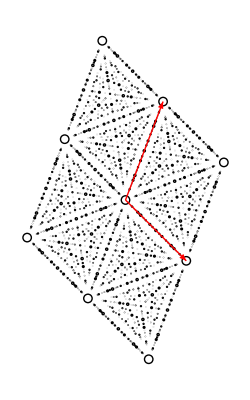

```mathematica
Show[intensityPlotGM[vqTableRecipGM[25,11],Sqrt[Sqrt[#]]*0.05&,clipCutGM],
Graphics[{Red,Arrow[{{0,0},DualGM.{0,1}}],Arrow[{{0,0},DualGM.{1,0}}]}]]
```